```mathematica
Quit[]
```

#### Kernels Control

```mathematica
Once[LaunchKernels[4]]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop,NIntegrate::slwcon]];
```

```mathematica
(*ParallelEvaluate[On[General::stop]];*)
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

```mathematica
ParallelEvaluate@SetOptions[NIntegrate,MaxRecursion->100,AccuracyGoal->10];
```

```mathematica
(*Old declaration, now packed into Package:OneFlavour`*)
```

The amplitude

```mathematica
(*If targeting the position, then use [ω1,ω2]*)
```

```mathematica
𝒞[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2,M1->M3,M3->M1,M2->M4,M4->M2}]
𝒫[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2,ϕ1->ϕ2,ϕ2->ϕ1,ϕ3->ϕ4,ϕ4->ϕ3,M1->M2,M2->M1,M3->M4,M4->M3}]
ℛ[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω1/ω2,ω2->1/ω2,ϕ3->ϕ4,ϕ4->ϕ3,M3->M4,M4->M3}]
𝒮[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1,ϕ1->ϕ4,ϕ4->ϕ1,ϕ2->ϕ3,ϕ3->ϕ2,M1->M4,M4->M1,M2->M3,M3->M2}]
```

```mathematica
EXPR[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}]
```

```mathematica
(*ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]);*)
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]}]+If[(-ω1+λ ω1+ω2)/ω2>0,NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,(-ω1+λ ω1+ω2)/ω2},{y,0,1}],0]+If[(-λ ω1+ω2)/ω2<1,NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,(-λ ω1+ω2)/ω2,1},{y,0,1}],0]);
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]}]+If[ω1 λ>0,NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,ω1 λ},{y,0,1}],0]+If[ω1 (1-λ)<1,NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,ω1 (1-λ),1},{y,0,1}],0]);
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+(m^2-β^2)/(x-ω1)+(m^2-β^2)/(x-1)-(m^2-β^2)/(x-ω1+ω2)-(m^2-β^2)/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}];
```

```mathematica
EXPR1[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md];
```

```mathematica
ℳone[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR1[ω1,ω2][m,Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-5;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
(*ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)*)
```

```mathematica
(*Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);*)
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine,Mseq,ΦBi},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"BSW method"->True,"Brute force integration"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
}
];
(*Set@@{ΦB[x_?NumberQ],If[0<x<1,ΦBi[x],Table[0,{n,Length@ϕxB}]]};*)
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Mseq=Sequence[M1,M2,M3,M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
{Ssqur,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][mQ,M1,M2,M3,M4]},{Ssqur,M1+M2,M1+M2+2,0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear["OneFlavour`"]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["OneFlavour`"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

```mathematica
AbsoluteTiming[Msumdat=Msum[60,{0,0,0,0},SRange->{10^-3,2,0.05}]]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,243},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,243},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{1,1,1,1},SRange->{10^-3,0.5,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.79  M2=120.79  M3=120.79  M4=120.79

{{120.79,120.79,120.79,120.79},{{241.581,-3644.33},{241.591,-4080.22},{241.601,-4405.19},{241.611,-4640.22},{241.621,-4796.55},{241.631,-4885.79},{241.641,-4918.78},{241.651,-4904.98},{241.661,-4852.53},{241.671,-4768.98},{241.681,-4660.8},{241.691,-4532.39},{241.701,-4389.52},{241.711,-4236.27},{241.721,-4075.68},{241.731,-3910.75},{241.741,-3744.11},{241.751,-3579.11},{241.761,-3415.28},{241.771,-3254.64},{241.781,-3099.72},{241.791,-2949.05},{241.801,-2805.56},{241.811,-2668.94},{241.821,-2540.75},{241.831,-2419.88},{241.841,-2305.19},{241.851,-2123.59},{241.861,-2021.75},{241.871,-1929.22},{241.881,-1929.26},{241.891,-1853.42},{241.901,-1785.21},{241.911,-1729.89},{241.921,2.31676×10^6},{241.931,-1620.99},{241.941,-1578.3},{241.951,-1540.01},{241.961,-1509.7},{241.971,-1482.02},{241.981,-1460.57},{241.991,-1441.75},{242.001,-1427.76},{242.011,-1417.06},{242.021,-1409.9},{242.031,-1405.49},{242.041,-1393.72},{242.051,-1394.6},{242.061,-1403.69},{242.071,-1408.74}}}

```mathematica
Msumdat=Msum[60,{1,1,1,1},SRange->{0.51,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.79  M2=120.79  M3=120.79  M4=120.79

{{120.79,120.79,120.79,120.79},{{242.09,-1429.09},{242.12,-1478.99},{242.15,-1503.38},{242.18,-1576.51},{242.21,-1611.9},{242.24,-1656.32},{242.27,-1701.19},{242.3,-1738.11},{242.33,-1737.88},{242.36,-1794.22},{242.39,-1812.97},{242.42,-1825.5},{242.45,-1832.43},{242.48,-1834.76},{242.51,-1831.2},{242.54,-1821.96},{242.57,-1808.44},{242.6,-1791.04},{242.63,-1770.25},{242.66,-1746.01},{242.69,-1719.35},{242.72,-1690.99},{242.75,-1658.39},{242.78,-1565.54},{242.81,-1596.93},{242.84,-1563.64},{242.87,-1529.7},{242.9,-1495.54},{242.93,-1461.22},{242.96,-1426.9},{242.99,-1392.83},{243.02,-1359.17},{243.05,-1325.87},{243.08,-789.649},{243.11,-1261.24},{243.14,-1230.02},{243.17,-1180.53},{243.2,-1169.13},{243.23,-1140.04},{243.26,-1111.56},{243.29,-1083.64},{243.32,-1056.81},{243.35,-1030.57},{243.38,-1005.35},{243.41,-980.937},{243.44,-957.04},{243.47,-934.454},{243.5,-912.366},{243.53,-891.029},{243.56,-870.396}}}

```mathematica
Msumdat={%7[[1]],%7[[2]]~Join~%8[[2]]};
```

```mathematica
Msumdat=Delete[Msumdat,{2,-17}];
```

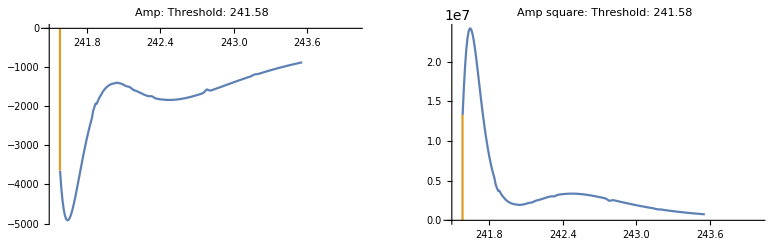

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,2,2,2},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=121.104  M4=121.104

{{121.104,121.104,121.104,121.104},{{242.208,-6484.36},{242.238,-7357.1},{242.268,-6895.85},{242.298,-6069.43},{242.328,-5318.48},{242.358,-4792.04},{242.388,-4499.01},{242.418,-4386.41},{242.448,-4377.6},{242.478,-4424.39},{242.508,-4483.5},{242.538,-4494.},{242.568,-4375.85},{242.598,-4348.73},{242.628,-4131.76},{242.658,-3983.77},{242.688,-3743.17},{242.718,-3474.83},{242.748,-3194.66},{242.778,-2912.18},{242.808,-2635.12},{242.838,-2377.78},{242.868,-2138.02},{242.898,-1922.07},{242.928,-1731.72},{242.958,-1568.03},{242.988,-1456.87},{243.018,-1317.68},{243.048,-1228.69},{243.078,-1169.7},{243.108,-1112.03},{243.138,-1078.66},{243.168,-1060.29},{243.198,-1053.15},{243.228,-1055.85},{243.258,-1075.79},{243.288,-1090.07},{243.318,-1105.3},{243.348,-1131.82},{243.378,-1142.9},{243.408,-1165.73},{243.438,-1188.04},{243.468,-1209.19},{243.498,-1228.38},{243.528,-1245.9},{243.558,-1260.4},{243.588,-1272.86},{243.618,-1282.28},{243.648,-1289.1},{243.678,-1293.28},{243.708,-1294.79},{243.738,-1285.12},{243.768,-1290.49},{243.798,-1285.01},{243.828,-1277.56},{243.858,-1268.22},{243.888,-1256.65},{243.918,-1244.43},{243.948,-1230.65},{243.978,-1215.24},{244.008,-1199.09},{244.038,-1182.02},{244.068,-1164.24},{244.098,-1145.89},{244.128,-1127.03},{244.158,-1107.86},{244.188,-1088.3}}}

```mathematica
Msumdat=Msum[60,{2,2,2,2},SRange->{10^-3,0.5,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=121.104  M4=121.104

{{121.104,121.104,121.104,121.104},{{242.208,-6484.36},{242.218,-7014.64},{242.228,-7281.77},{242.238,-7357.1},{242.248,-7242.48},{242.258,-7076.02},{242.268,-6895.85},{242.278,-6631.67},{242.288,-6350.83},{242.298,-6069.43},{242.308,-5800.67},{242.318,-5547.02},{242.328,-5318.48},{242.338,-5113.45},{242.348,-4939.82},{242.358,-4792.04},{242.368,-4670.32},{242.378,-4573.73},{242.388,-4499.01},{242.398,-4446.39},{242.408,-4406.23},{242.418,-4386.41},{242.428,-4377.},{242.438,-4377.49},{242.448,-4377.6},{242.458,-4391.22},{242.468,-4407.22},{242.478,-4424.39},{242.488,-4455.13},{242.498,-4470.59},{242.508,-4483.5},{242.518,-4491.92},{242.528,-4495.58},{242.538,-4494.},{242.548,-4485.36},{242.558,-4471.84},{242.568,-4375.85},{242.578,-4403.08},{242.588,-4389.55},{242.598,-4348.73},{242.608,-4301.88},{242.618,-4248.87},{242.628,-4131.76},{242.638,-4126.18},{242.648,-4056.67},{242.658,-3983.77},{242.668,-3908.15},{242.678,-3825.91},{242.688,-3743.17},{242.698,-3655.18}}}

```mathematica
Msumdat={%12[[1]],%12[[2]]~Join~Drop[%9[[2]],17]};
```

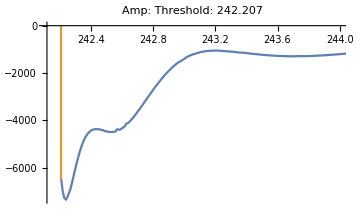
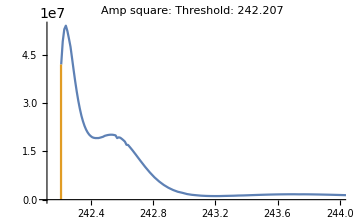

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

### Debug

```mathematica
Clear[ValsB,ϕxB,ΦB,ΦBi];
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBi[x_?NumberQ],If[0<x<1,ΦB[x],Table[0,{n,Length@ϕxB}]]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];]
```

Wavefunction build complete.

```mathematica
Block[{ω1,S,ω2,λ=10^-6},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];(-ω1+λ ω1+ω2)/ω2]
```

-0.0544286

```mathematica
?ℳ1
```

Global`ℳ1

ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]:=(#1+𝒮[#1]&)[ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]+(#1+𝒞[#1]&)[ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]+(#1+𝒮[#1]+𝒫[#1]+𝒞[#1]&)[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]

```mathematica
ParallelTable[ℳ1[ω1,ω2p[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1,0.1,0.9,0.1}]
```

{1.78558×10^-7,1.65793×10^-6,0.0000101498,0.0000577362,0.000373372,0.00330655,0.0592053,8.32501,889.414}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
{√S,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

{240.681,-6.18205×10^48-1.74609×10^13 ⅈ}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

-1.22158×10^87

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

8225.61

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

15.7

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

16256.1

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]]
```

-14092.9

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

8319.93

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];
ℐ1[1,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3957.52

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999654854344164204888074920507534670832683332264423370361328125,0.0000554132}. NIntegrate obtained 8.84168×10^90 and 8.42964×10^90 for the integral and error estimates.

-3.53668×10^91

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3957.53

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999654854344164204888074920507534670832683332264423370361328125,0.0000554132}. NIntegrate obtained 8.84168×10^90 and 8.42964×10^90 for the integral and error estimates.

-3.53668×10^91

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000257322,0.999448629114065381444896585261261634514085017144680023193359375}. NIntegrate obtained 1.99029×10^90-1.56519×10^77 ⅈ and 4.57862×10^90 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-7.96119×10^90+9.01471×10^71 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-1.4358×10^90

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-1/λ 2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,x/(ω2/(1-ω1+ω2))+λ,1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-989.382

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,0,1}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,x/ω1+λ,1}]]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99695296594626931462046481868810587911866605281829833984375,6.53456×10^-6}. NIntegrate obtained -2.10878×10^8 and 3.42692×10^7 for the integral and error estimates.

-2.12991×10^8

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,ω1 λ},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),1},{y,0,1}]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.98193325930478849855469612529286927565808085205389943439513444901,0.99999996542503735904070120079855884566433221749548465595580637455}. NIntegrate obtained 87316.5 and 205136. for the integral and error estimates.

-1.84108×10^6

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),1},{y,0,1}]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.98193325930478849855469612529286927565808085205389943439513444901,0.99999996542503735904070120079855884566433221749548465595580637455}. NIntegrate obtained 87316.5 and 205136. for the integral and error estimates.

87316.5

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-868.613,-980.246,-991.512,-992.625,-989.382,-992.32,-9669.95,3911.96,-31558.7}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-1.4358×10^90

```mathematica
ϕ2[-0.0001]
```

8.05448×10^-15+3.52344×10^-6 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4,x=0.99,y},y=0.99;S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Print@y;Print@ ϕ4[(x+ω2-ω1)/(1+ω2-ω1)];(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2]
```

0.99

-4.14082×10^-6

9.02401×10^-19

```mathematica
ϕ2[1.0184001182742242]
```

0

```mathematica
λ=10^-5;
```

```mathematica
ParallelTable[{x,Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1)/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,x/ω1+λ,1}]]},{x,(Sin[π #]^9/2+0.5)&/@Range[0,1,0.01]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0161417755171127605127677620338796926624524985527386888861656189}. NIntegrate obtained 1.93215×10^86 and 3.52905×10^85 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0161417755171127605127677620338796926624524985527386888861656189}. NIntegrate obtained 1.93215×10^86 and 3.52905×10^85 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0094267645357584649047232619152938970508159854944096878170967102}. NIntegrate obtained 4.93962×10^62 and 4.71021×10^62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0094267645357584649047232619152938970508159854944096878170967102}. NIntegrate obtained 4.93962×10^62 and 4.71021×10^62 for the integral and error estimates.

{{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.2},{0.500001,-35283.5},{0.500002,-35281.3},{0.500005,-35275.5},{0.500013,-35262.1},{0.500029,-35233.4},{0.500062,-35176.3},{0.500123,-35069.5},{0.50023,-34879.6},{0.50041,-34555.4},{0.500699,-34019.7},{0.501147,-33156.4},{0.50182,-31793.3},{0.5028,-29682.5},{0.504187,-26495.8},{0.506103,-21878.4},{0.508686,-15649.7},{0.512096,-8228.56},{0.516504,-1108.86},{0.522097,3410.12},{0.529064,4054.62},{0.537592,2312.74},{0.547862,746.702},{0.560032,147.699},{0.574232,20.6585},{0.590552,2.46605},{0.609036,0.29785},{0.629666,0.0405149},{0.652361,0.0064289},{0.676969,0.00118187},{0.703264,0.000246994},{0.730945,0.0000575922},{0.759643,0.0000147441},{0.788922,4.08674×10^-6},{0.818293,1.2106×10^-6},{0.847222,3.78288×10^-7},{0.875148,1.22916×10^-7},{0.901499,4.07948×10^-8},{0.925713,1.35412×10^-8},{0.947249,4.34482×10^-9},{0.965615,1.27855×10^-9},{0.98038,3.13312×10^-10},{0.99119,4.94241×10^62+0. ⅈ},{0.997784,1.94269×10^86+0. ⅈ},{1.,0.+0. ⅈ},{0.997784,1.94269×10^86+0. ⅈ},{0.99119,4.94241×10^62+0. ⅈ},{0.98038,3.13312×10^-10},{0.965615,1.27855×10^-9},{0.947249,4.34482×10^-9},{0.925713,1.35412×10^-8},{0.901499,4.07948×10^-8},{0.875148,1.22916×10^-7},{0.847222,3.78288×10^-7},{0.818293,1.2106×10^-6},{0.788922,4.08674×10^-6},{0.759643,0.0000147441},{0.730945,0.0000575922},{0.703264,0.000246994},{0.676969,0.00118187},{0.652361,0.0064289},{0.629666,0.0405149},{0.609036,0.29785},{0.590552,2.46605},{0.574232,20.6585},{0.560032,147.699},{0.547862,746.702},{0.537592,2312.74},{0.529064,4054.62},{0.522097,3410.12},{0.516504,-1108.87},{0.512096,-8228.56},{0.508686,-15649.7},{0.506103,-21878.4},{0.504187,-26495.8},{0.5028,-29682.5},{0.50182,-31793.3},{0.501147,-33156.4},{0.500699,-34019.7},{0.50041,-34555.4},{0.50023,-34879.6},{0.500123,-35069.5},{0.500062,-35176.3},{0.500029,-35233.4},{0.500013,-35262.1},{0.500005,-35275.5},{0.500002,-35281.3},{0.500001,-35283.5},{0.5,-35284.2},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4}}

```mathematica
Drop[%75,-1]
```

{{0.98038,3.13312×10^-10},{0.965615,1.27857×10^-9},{0.947249,4.34508×10^-9},{0.925713,1.35439×10^-8},{0.901499,4.08177×10^-8},{0.875148,1.22916×10^-7},{0.847222,3.78288×10^-7},{0.818293,1.2106×10^-6},{0.788922,4.08674×10^-6},{0.759643,0.0000147441},{0.730945,0.0000575922},{0.703264,0.000246994},{0.676969,0.00118187},{0.652361,0.0064289},{0.629666,0.0405149},{0.609036,0.297849},{0.590552,2.46603},{0.574232,20.6581},{0.560032,147.691},{0.547862,746.617},{0.537592,2312.3},{0.529064,4053.46},{0.522097,3408.38},{0.516504,-1110.39},{0.512096,-8229.04},{0.508686,-15648.8},{0.506103,-21876.2},{0.504187,-26492.5},{0.5028,-29678.5},{0.50182,-31788.7},{0.501147,-33151.5},{0.500699,-34014.6},{0.50041,-34550.1},{0.50023,-34874.2},{0.500123,-35064.1},{0.500062,-35170.8},{0.500029,-35227.9},{0.500013,-35256.6},{0.500005,-35270.1},{0.500002,-35275.8},{0.500001,-35278.},{0.5,-35278.7},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35279.},{0.5,-35279.},{0.5,-35279.2},{0.499999,-35279.9},{0.499998,-35282.1},{0.499995,-35287.8},{0.499987,-35301.2},{0.499971,-35329.8},{0.499938,-35386.2},{0.499877,-35490.5},{0.49977,-35672.1},{0.49959,-35971.1},{0.499301,-36436.6},{0.498853,-37118.9},{0.49818,-38047.5},{0.4972,-39182.5},{0.495813,-40319.6},{0.493897,-40932.3},{0.491314,-39983.8},{0.487904,-35930.9},{0.483496,-27478.6},{0.477903,-15529.2},{0.470936,-4592.52},{0.462408,615.327},{0.452138,925.964},{0.439968,266.456},{0.425768,38.5137},{0.409448,4.10866},{0.390964,0.44148},{0.370334,0.0553202},{0.347639,0.00829998},{0.323031,0.0014655},{0.296736,0.000297087},{0.269055,0.0000676543},{0.240357,0.0000169991},{0.211078,4.64163×10^-6},{0.181707,1.3584×10^-6},{0.152778,4.20312×10^-7},{0.124852,1.3548×10^-7},{0.0985005,4.47008×10^-8},{0.0742873,1.47534×10^-8},{0.052751,4.71341×10^-9},{0.034385,1.38245×10^-9},{0.0196203,3.37947×10^-10},{0.00880996,5.55903×10^-11},{0.0022161,3.1151×10^-12}}

```mathematica
NIntegrate[Interpolation[%80][x],{x,0,1}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 1 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-991.682

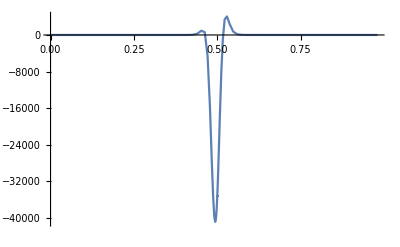

```mathematica
ListPlot[%80,Joined->True,PlotRange->All]
```

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

-14092.9

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]]
```

3.83865

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1]]
```

3.83865

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2]]
```

0.981933

-3.35036×10^80+1.31763×10^67 ⅈ

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]]
```

0

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

-1.62385

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.999409304759193060376486206219937002970254980027675628662109375,0.0000129484} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26099×10^209 和 2.18188×10^209.

5.04402×10^209

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 (NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]]
```

0

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},MaxRecursion->50]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 5.54003×10^6 和 4.90296×10^6.

5.54003×10^6

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,(x (1-ω1+ω2))/ω2-λ}]]
```

1.30171×10^183

```mathematica
Block[{ω1,S,ω2,ex},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ex=(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1];NIntegrate[ex,{x,0,1},{y,(x (1-ω1+ω2))/ω2+λ,1},MaxRecursion->50,PrecisionGoal->15]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.10072×10^213 和 2.99925×10^206.

-1.10072×10^213

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];(2 NIntegrate[(ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[(x (1-ω1+ω2))/ω2] ϕ3[x] ϕ4[(x+ω1-x ω1-ω2+x ω2)/ω1])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ]
```

2.68909×10^200

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2),{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

2.13307×10^6

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.000590695,0.99998705161026963496755440557323124650679346814285963773727416992} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.25434×10^209-9.59962×10^195 ⅈ 和 2.17036×10^209.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

-5.0174×10^209+4.18059×10^191 ⅈ

```mathematica
Clear[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
SetSharedVariable[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
Table[{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]],{n1,0,5,1},{n2,0,5,1}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

$Aborted

```mathematica
ParallelTable[ℳ1[M1,M2,M3,M4][ω1/(ω2p[ω1][M1,M2,M3,M4]),1/(ω2p[ω1][M1,M2,M3,M4])][ϕ1,ϕ2,ϕ3,ϕ4],{ω1,0.1,0.9,0.1}]
```

{3.57115×10^-7,3.31586×10^-6,0.0000202997,0.000115472,0.000746742,0.00661315,0.118411,16.65,1778.83}

```mathematica
?EXPR
```

Global`EXPR

EXPR[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2),((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]

```mathematica
FindRoot[√(Sω1[ω1][M1,M2,M3,M4])==241.137,{ω1,0.9,0.99}]
```

{ω1→0.882942}

```mathematica
Reduce[1/(ω2p[ω1][M1,M2,M3,M4])>(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])&&(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])>1,ω1]
```

$Aborted

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[ω2>ω1&&ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
ω1/.FindInstance[ω2p[ω1][M1,M2,M3,M4]>ω1&&ω1>1&&0<ω1<1,ω1,100]
```

ω1

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; Print[1/ω2>(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])&&(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])>1&&0<ω1<1];NIntegrate[(M3^2+M4^2/(ω1/(1-ω1+ω2))+M1^2/(x-ω2/(1-ω1+ω2))+M1^2/(x-1)-M1^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-M1^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}]]
```

False

8.83407707562666×10^916

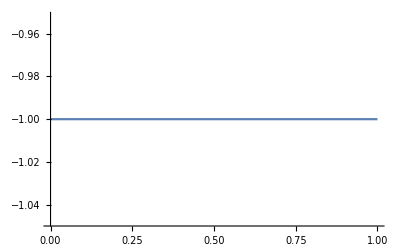

```mathematica
Plot[ω2n[ω1][M1,M2,M3,M4],{ω1,0,1}]
```

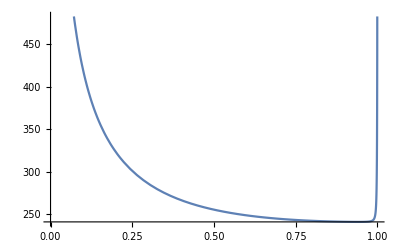

```mathematica
Plot[√(Sω1[ω1][M1,M2,M3,M4]),{ω1,0,1}]
```

```mathematica
Block[{ω1=0.8829424796893336,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]]
```

1955.93

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.708776

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

NIntegrate::ncvb: 在接近 {x,y} = {0.526042,0.410879} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

{244.244,-113404.}

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.09278

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

-3.46707×10^259

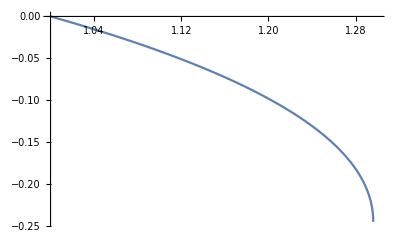

```mathematica
Plot[(ω2p[ω1][M1,M2,M3,M4])/ω1,{ω1,1,1.3}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.429446,0.907482} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -9.1960468217209363414030970359671991396517715069998422535022594849×10^1780+6.6644443576245410010334590115150447725581246899922275744416000763×10^1767 ⅈ 和 2.8418655168893182884967858465873180630766840277546920593796254944×10^1780.

-9.19604682172094×10^1780+6.7×10^1767 ⅈ

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

4.33383×10^258

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
λ=10^-4;
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

$Aborted

```mathematica
Table[Block[{ω1=0.3,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,0,x-λ}]+NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,x+λ,1}]-2/λ NIntegrate[ ϕ1[x ω2]ϕ2[x]ϕ3[x ω1]ϕ4[x],{x,λ,1-λ}])],{λ,Table[10^-m,{m,2,7,1}]}]
```

{19.4562,19.7495,19.7852,19.7698,19.711,19.3019}

-7.96119×10^90+9.01471×10^71 ⅈ